# xlr8r example

ring-oscillator-GRN.nb

revised 10-15-07 (BES) to work under Mathematica 6.0

## GRN-baesd ring oscillator

```mathematica
<<xlr8r.m
```

xlr8r 0.20 (11-August-2005) loaded 11-August-2005 17:46:33.695757 using Mathematica 5.2 for Mac OS X (June 20, 2005)

```mathematica
Clear[n]
```

```mathematica
reactions={
{U↦V,GRN[1/tau,-1,n,h, sigmoid]},
{V↦W,GRN[1/tau,-1,n,h, sigmoid] }, 
{W↦U,GRN[1/tau,-1,n,h, sigmoid] }, 

{V-> ∅,k}, {U-> ∅,k}, {W-> ∅,k}}
```

{{U↦V,GRN[1/tau,-1,n,h,sigmoid]},{V↦W,GRN[1/tau,-1,n,h,sigmoid]},{W↦U,GRN[1/tau,-1,n,h,sigmoid]},{V→∅,k},{U→∅,k},{W→∅,k}}

```mathematica
odes=interpret[reactions]
```

{{U'[t]==1/((1+ⅇ^(-h+W[t]^n)) tau)-k U[t],V'[t]==1/((1+ⅇ^(-h+U[t]^n)) tau)-k V[t],W'[t]==1/((1+ⅇ^(-h+V[t]^n)) tau)-k W[t]},{U,V,W}}

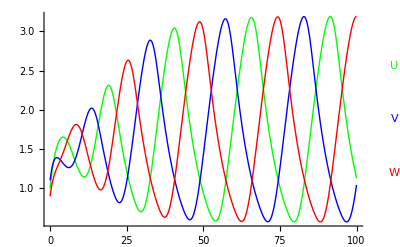

{{U→InterpolatingFunction[{{0.,100.}},<>],V→InterpolatingFunction[{{0.,100.}},<>],W→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
myrates={tau-> 1, n-> 2, h-> 1, k-> .15};
sim=run[odes, timeSpan-> 100,initialConditions-> {U-> 1, V->1.1, W-> .9}, rates-> myrates, plot-> True]
```